```mathematica
?Graph
```

Graph[{e_1,e_2,…}] yields a graph with edges e_j.
Graph[{v_1,v_2,…},{e_1,e_2,…}] yields the graph with vertices v_i and edges e_j. 
Graph[{…,w_i[v_i,…],…},{…,w_j[e_j,…],…}] yields a graph with vertex and edge properties defined by the symbolic wrappers w_k.

```mathematica
g=Graph[Range[9],Transpose[{Range[1,9],Range[2,9]~Join~{1}}]~Join~{{1,4},{4,2},{2,8},{8,5},{5,7},{7,1}}~Join~{{3,6},{6,9},{9,3}}]
```

```mathematica
PlanarGraphQ[g]
```

False

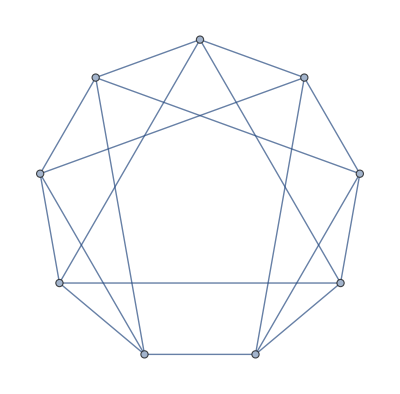

```mathematica
Transpose[{Range[1,9],Range[2,9]~Join~{1}}]
```

{{1,2},{2,3},{3,4},{4,5},{5,6},{6,7},{7,8},{8,9},{9,1}}

```mathematica
Transpose[{{1,4,2,8,5,7},{4,2,8,5,7,1}}]
```

{{1,4},{4,2},{2,8},{8,5},{5,7},{7,1}}